dayAngle[day of month, month, year] returns optimal angle for this day

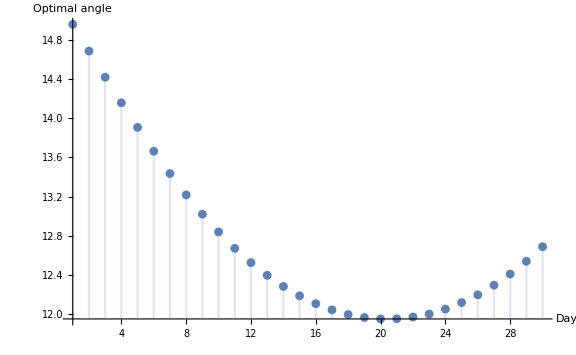

```mathematica
(* Graph for a month, adjusting one time per day *)
<<SolArduino`
?dayAngle
 month = 6;
days = With[{first=DateObject[{year,month,1}]},DayCount[first,DatePlus[first,{{1,"Month"}}]]];
DiscretePlot[dayAngle[a,month,2016],{a,1,days},ImageSize->Large,AxesLabel -> {"Day", "Optimal angle"}]
```

monthAngle[month, year] returns optimal angle for a specific month by taking the average of the optimal angle each day

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

{75.8754,67.4699,54.7956,37.1887,21.2384,12.7559,17.3159,31.5787,49.223,63.7122,73.67,78.1485}

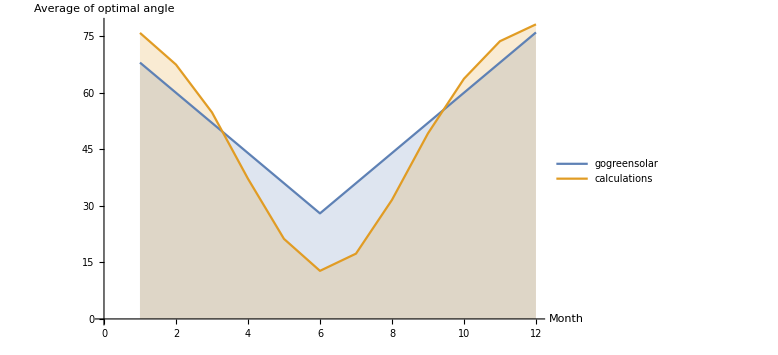

```mathematica
(* Comparison with perpendicular to sun at noon, per month, http://www.gogreensolar.com/pages/solar-panel-tilt-calculator *)
<< SolArduino`
?monthAngle
greenList = {68,60,52,44,36,28,36,44,52,60,68,76};
list = Table[monthAngle[x,2016],{x,1,12}]
ListLinePlot[{greenList,list},Filling-> Axis,PlotLegends-> {"gogreensolar","calculations"},ImageSize->Large,AxesLabel -> {"Month", "Average of optimal angle"}]
```

```mathematica
(* season values *)
<< SolArduino`
year = 2016;
monthSum[m_,i_,j_] := ( (* month, begin day, end day *)
Sum[
Quiet[dayAngle[x,m,year]],
{x,i,j}]
)
(* takes winter of [year] only. dates according to solarpaneltilt.com, summer april 18, autumn august 24, winter oct 7, spring march 5 *)
 summerSum = Quiet[monthSum[4,18,30] + monthSum[5,1,31] + monthSum[6,1,30] + monthSum[7,1,31]+ monthSum[8,1,23]];
summerDays = QuantityMagnitude[Quantity[DateDifference[{year,4,18},{year,8,23}]]]+1;
summerSum/summerDays (* 21 degrees *)

autumnSum = monthSum[8,24,31]+ monthSum[9,1,30] + monthSum[10,1,6];
autumnDays = DayCount[{year,8,24},{year,10,6}]+1;
autumnSum/autumnDays (* 49 degrees *)

 winterSum = Quiet[monthSum[10,7,31] + monthSum[11,1,30] +monthSum[12,1,31] + monthSum[1,1,31] + monthSum[2,1,29] + monthSum[3,1,4]];
winterDays = DayCount[{year,10,7},{year+1,3,4}]+1;
winterSum/winterDays  (* 73 degrees *)

springSum = Quiet[monthSum[3,5,31] + monthSum[4,1,17]];
springDays = DayCount[{year,3,5},{year,4,17}]+1;
springSum/springDays (* 49 degrees *)

(* Year average *)
(winterSum + summerSum + springSum + autumnSum)/366 (* 49 degrees *)
(* standalone *)
(*Sum[
days = With[{first=DateObject[{year,m,1}]},DayCount[first,DatePlus[first,{{1,"Month"}}]]];
Sum[
Quiet[dayAngle[d,m]]
,{d,1,days}]
,{m,1,12}]/ QuantityMagnitude[Quantity[DateDifference[{year,1,1},{year,12,31}]]]+1 (* 50 degrees *)
*)
```

20.8601

48.4822

72.5455

48.9036

48.5365

dayAngle[day of month, month, year] returns optimal angle for this day

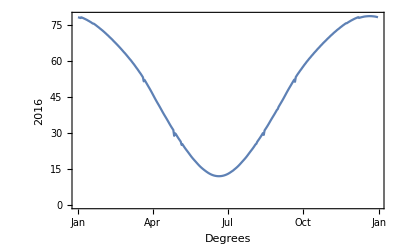

```mathematica
(* Full graph of year *)
<< SolArduino`
?dayAngle
year = 2016;
numberOfDays = DayCount[DateObject[{year,1,1}],DateObject[{year+1,1,1}]];
dateByDay=Function[x,DateObject[{year,1,1}]+Quantity[(x-1),"Days"]];

t = Table[{dateByDay[d],Quiet[dayAngle[DateValue[dateByDay[d],"Day"],DateValue[dateByDay[d],"Month"],year]]},{d,1,numberOfDays}];
DateListPlot[t,AxesLabel -> {"Degrees","2016"}]
```

{{38.9735,54.7261},{254.734,52.1053},{612.696,50.1369},{873.733,48.0889},{1033.03,45.853},{1118.3,43.2855},{1146.28,40.1852},{1660.85,34.9526},{993.106,27.2792},{837.73,17.3171},{647.221,0.819512},{435.721,0.},{200.062,0.},{80.8025,0.}}

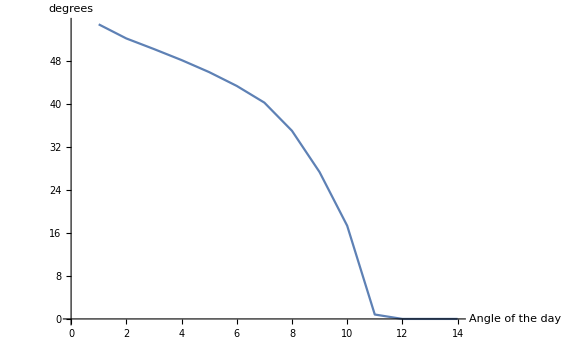

```mathematica
(* angle over the day *)
<<SolArduino`
calculatesunPos[DateObject[{2016,8,17}]]
res = dayAngles[DateObject[{2016,8,17}],14]
ListLinePlot[Table[res[[i]][[2]] ,{i,1,Length[res]}],AxesLabel -> {"Angle of the day","degrees"},ImageSize -> Large]
```

{9144.18,9561.69,9873.62,9882.66,9885.25,9894.52,9924.12,9921.82,9914.93,9924.79}

{0.0456588,0.0797716,0.0807601,0.0810428,0.0820569,0.0852942,0.0850424,0.0842891,0.0853679}

{0.0456588,0.0326232,0.000915529,0.000261591,0.000938063,0.0029918,-0.000232073,-0.000694221,0.000994926}

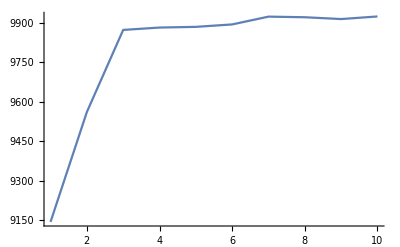

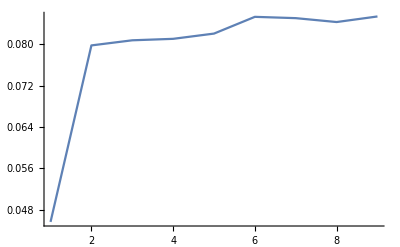

```mathematica
(* Plot of power increase when adjusting more times a day *)
<<SolArduino`
calculatesunPos[DateObject[{2016,8,17}]]
(* percentages *)
t = Table[
dayPower[dayAngles[DateObject[{2016,8,17}],x]],
{x,1,10}
]
(* relative to first *)
s =Table[
(t[[i]]-t[[1]])/t[[1]],
{i,2,Length[t]}
]
(* relative to previous *)
Table[
(t[[i]]-t[[i-1]])/t[[i-1]],
{i,2,Length[t]}
]
ListLinePlot[ t,PlotRange -> All] 
ListLinePlot[ s,PlotRange -> All]
```

```mathematica
(* list of angles for a day *)
<<SolArduino`
calculatesunPos[DateObject[{2016,8,17}]]
?dayAngles
dayAngles[DateObject[{2016,8,17}],14][[All,2]]
```

dayAngles[date, number of adjustment times per day ≥ 1] returns List with optimal angles and power received with that angle over each interval (spread evenly over the day) after an angle adjustment

{54.7261,52.1053,50.1369,48.0889,45.853,43.2855,40.1852,34.9526,27.2792,17.3171,0.819512,0.,0.,0.}

angle[index of sunPositions table, solar panel angle in degrees, date (date object)] returns misalignment with the sun in radians

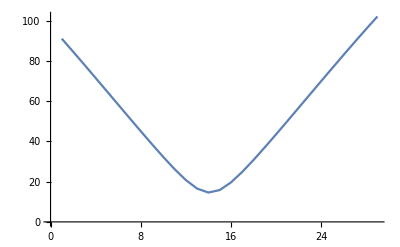

```mathematica
(* misalignment over day *)
<<SolArduino`
calculatesunPos[DateObject[{2016,8,17}]]
?angle
ListLinePlot[Table[
angle[i,25,DateObject[{2016,8,17}]]*180/Pi
,{i,1,getSunPositionsLength[]}
]]
```

directPower[index of sunPositions table, solar panel angle in degrees, date (date object)] returns power that the solar panels receive from the sun in  W/m^2

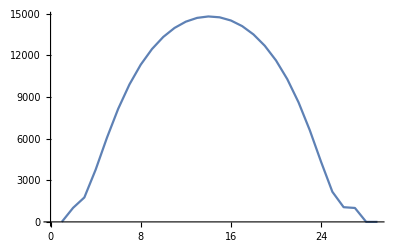

```mathematica
(* sun insolation over day, 26.4 m2 panels *)
<<SolArduino`
calculatesunPos[DateObject[{2016,8,17}]]
?directPower
ListLinePlot[Table[
directPower[i,25,DateObject[{2016,8,17}]]*26.4
,{i,1,getSunPositionsLength[]}
]]
```

initialiseSunPositionByPrecision[date,precision (hours*100)] initializes sunPositions table with positions of the sun for this day

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

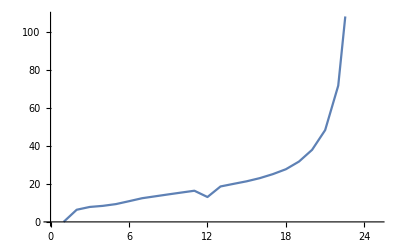

```mathematica
(* efficiency over the day for adjusting once a day *)
<< SolArduino`
(*date = DateObject[{2016,8,17}];
ListLinePlot[
calculatesunPos[date];
Table[
dataAugust[[i]]*100/(directPower[i,dayAngle[17,8,2016],date]*26.4)
,{i,1,getSunPositionsLength[]}
]
]*)
(* efficiency adjusting every hour *)
(*data = Import[ NotebookDirectory[]<>"data24_30.csv"];
data = Delete[data,1];
?csvToList
date = DateObject[{2016,8,30}];
data3008 = csvToList[date,data]*)
data3008 = {0,95.8333,280.6667,514.5,785,1117.5,1465,1740,1997.5,2230.8333,2440,1979.75,2830.3333,3014.3333,3151.5,3280.5,3400,3479.6667,3580.5,3657.1667,3679.5,3735,3777.1667,3794.3333,3789,3769.8333,3730.1667,3678.5,3628.5,3543.5,3468.3333,3375.5,3246,3148,3000.3333,2843.5,2700.5,2578.5,2368.3333,2089.6667,1901.6666,1768.8334,1615.8334,1363,1082.5,879.8333,752.5,597.3333,349,187.6667,127.1667,97.3333,75.8333,41.6667,6.3333};
?initialiseSunPositionByPrecision
initialiseSunPositionByPrecision[date,25];
(*Length[data3008]
getSunPositionsLength[]*)
ListLinePlot[
calculatesunPos[date];
Table[
data3008[[i]]*100/(directPower[i,dayAngle[30,8,2016],date]*26.4)
,{i,1,getSunPositionsLength[]}
]
]
```

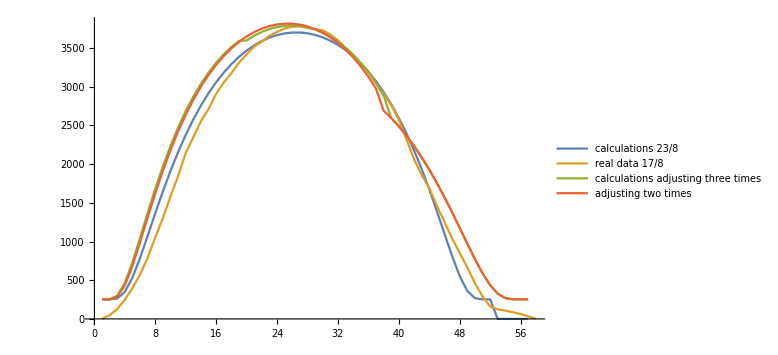

```mathematica
(* now for adjusting panels three times a day! *)
(* for 17/8, optimal angles and times are: 50,34,0 at 6.5, 11.3, 16.2, but directPower takes indices of sunPosition  *)
<<SolArduino`

factor = 6.7;
date = DateObject[{2016,8,23}];
initialiseSunPositionByPrecision[date,25]; (* initialise sunPositions with precision of real data *)
(* three plots *)
ListLinePlot[ {

Table[
directPower[i,25,date]*factor
,{i,1,getSunPositionsLength[]}
],

dataAugust,

Join[
Table[
directPower[i,49,date]*factor
,{i,1,Round[getSunPositionsLength[]/3]}
],
Table[
directPower[i,34,date]*factor
,{i,Round[getSunPositionsLength[]/3]+1,Round[getSunPositionsLength[]*2/3]}
],
Table[
directPower[i,0,date]*factor
,{i,Round[getSunPositionsLength[]*2/3]+1,getSunPositionsLength[]}
]
],

Join[
Table[
directPower[i,41,date]*factor
,{i,1,Round[getSunPositionsLength[]9/14]} (*16:00 is around 9/14  *)
],
Table[
directPower[i,0,date]*factor
,{i,Round[getSunPositionsLength[] 9/14]+1,getSunPositionsLength[]}
]
]

},PlotLegends -> {"calculations 23/8","real data 17/8","calculations adjusting three times", "adjusting two times"},ImageSize -> Large
]
```

```mathematica
(* two adjustment times, optimised *)
<<SolArduino`
?twoAnglesOptimal
twoAnglesOptimal[DateObject[{2016,6,20}]] 
twoAnglesOptimal[DateObject[{2016,12,20}]]
```

twoAnglesOptimal[date] returns in a list the date/time at which to change the angle of solar panels (besides before sunrise) 			to get optimal power, then the two angles of the day, then the percent increase of power compared to 			one setting for the whole day, then the percent increase compared to one setting if you would adjust 			fourteen times a day, spread evenly over the day

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{Mon 20 Jun 2016 15:43GMT+2.,{27.9359,0.},7.72683,8.63226}

FindMaximum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a maximum; it may be a minimum or a saddle point.

{Tue 20 Dec 2016 13:42GMT+2.,{81.2945,75.5525},0.106733,-8.17048}

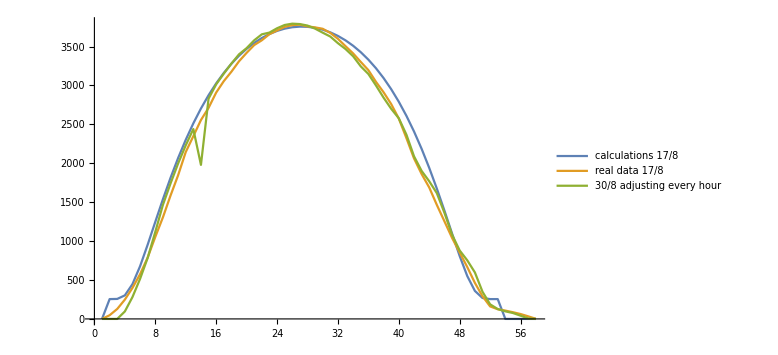

```mathematica
(* plot for one day, times 6.7 to compare form of graph *)
<< SolArduino`
(* data adapted to from sunrise, 6:33, to sunset, 21:00. Length of sunPositions and data are both 58 *)
(* day = DateObject[{2016,8,17}]; *)
dataAugust = {0,47.5,128.167,247.833,398.167,574.333,789,1053.83,1304.83,1584.33,1846.17,2144,2348.33,2555.83,2712,2908.67,3055.33,3176.33,3310.33,3419.17,3519.17,3580.67,3659.33,3707.17,3753.17,3775.17,3781,3759.5,3746.17,3728.5,3675,3599.67,3504.67,3411.83,3302.83,3197.33,3046.5,2912.83,2761.17,2574.83,2324.33,2062.5,1862.17,1688.83,1465,1254,1041.5,853.167,666,463,291.833,160.667,124.333,106.833,86,62.8333,33.3333,2};
(* day = DateObject[{2016,5,13}]; *)
dataMay = {0,19.5,57,118.667,200.833,278,301.333,497.667,691.5,995.667,1323.5,1663,1857.33,2262.67,2571,2789.83,3003,3177.5,3324.5,3483.17,3597,3719.33,3813.67,3888,3929.83,3997.83,4012.33,4036,4080.5,4067.67,4034,3957.67,3954.33,3889.17,3837,3746.83,3641.67,3453.33,3423.67,3215.5,3121.83,2954.5,2762.67,2541,2298.83,2055.33,1692,1540.17,1253,1027.17,782,579,419.5,295,226.833,185.833,158.667,115,84.5,70.1667,58.1667,20.1667,0};
(* 30/8, adjusting every hour *)
data3008 = {0,0,0,95.8333,280.6667,514.5,785,1117.5,1465,1740,1997.5,2230.8333,2440,1979.75,2830.3333,3014.3333,3151.5,3280.5,3400,3479.6667,3580.5,3657.1667,3679.5,3735,3777.1667,3794.3333,3789,3769.8333,3730.1667,3678.5,3628.5,3543.5,3468.3333,3375.5,3246,3148,3000.3333,2843.5,2700.5,2578.5,2368.3333,2089.6667,1901.6666,1768.8334,1615.8334,1363,1082.5,879.8333,752.5,597.3333,349,187.6667,127.1667,97.3333,75.8333,41.6667,6.3333,0};
(*Length[dataAugust]
Length[data3008]*)
ListLinePlot[{
initialiseSunPositionByPrecision[DateObject[{2016,8,17}],25];
Table[
directPower[i,25,DateObject[{2016,8,17}]]*6.7
,{i,1,getSunPositionsLength[]}
]
,dataAugust,data3008},PlotLegends -> {"calculations 17/8","real data 17/8","30/8 adjusting every hour"},ImageSize -> Large]
```

powerOverDay[list of angles of a day, date] returns a list with power received for each angle-period

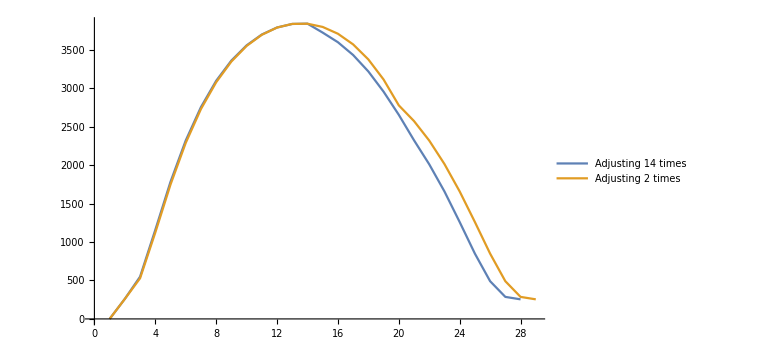

```mathematica
(* plot to compare 14 times with 2 times optimised *)
<< SolArduino`
?powerOverDay
date = DateObject[{2016,8,17}];
calculatesunPos[date];
factor = 6.7;
angles =dayAngles[date,14][[All,2]];
(* prepare legend for graph *)
legend=StringForm["Adjusting `` times", Length[angles]];

ListLinePlot[{powerOverDay[angles,date]*factor,

Join[
Table[
directPower[i,41,date]*factor
,{i,1,Round[getSunPositionsLength[]9/14]} (* 16:00 is around 9/14  *)
],
Table[
directPower[i,0,date]*factor
,{i,Round[getSunPositionsLength[] 9/14]+1,getSunPositionsLength[]}
]
]

}, ImageSize->Large, PlotLegends->{legend,"Adjusting 2 times"}]
```

Infinity::indet: Indeterminate expression 0.740741^ComplexInfinity encountered.

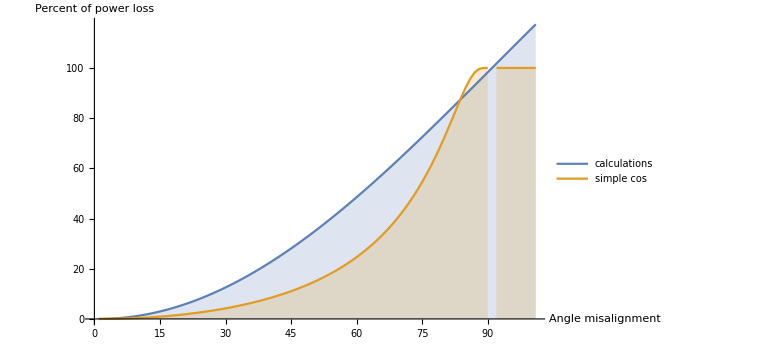

```mathematica
(******************* percent difference by angle ******************************)
<< SolArduino`
(*directPowerPercent := Function[ (* convert power to a percent loss *)
(1-directPower[#1,30,DateObject[{2016,6,20}]]/580)*100
]*)
solarPanelTilt[z_] := (
If[z>90,
100,
i =1.35*(1/1.35)^(Sec[z*Pi/180]);
(1-i)*100
]
)

(* DiscretePlot[directPower[x,30,DateObject[{2016,6,20}]],{x,1,20},ImageSize->Large] *)

ListLinePlot[{
Table[100*(1-Cos[x*Pi/180]),{x,0,100}],
Table[solarPanelTilt[x],{x,0,100}]},Filling -> Axis,PlotLegends -> {"calculations","simple cos","solarpaneltilt.com"},ImageSize -> Large,AxesLabel-> {"Angle misalignment","Percent of power loss"}]
```

```mathematica
(* exporting *)
<< SolArduino`
?anglesPeriod
t = anglesPeriod[DateObject[{2016,8,21}],DateObject[{2016,8,23}]]
(* Convert all the DateObjects to YYYY-MM-DD *)
Do[
t[[i,1]] = 
DateString[t[[i,1]],{"Year","-","Month","-","Day"}],
{i,Length[t]}
];
(* Export the table to csv, format YYYY-MM-DD, angle *)
Export[ NotebookDirectory[]<>"export.csv", t];
```

anglesPeriod[begin date, end date] creates list of optimal angles per day over given interval

{{Sun 21 Aug 2016,34.2879},{Mon 22 Aug 2016,34.8863},{Tue 23 Aug 2016,35.4718}}

dayAnglesHour[date] returns a list of {power output, optimal angle} at each whole hour of the time the sun is up

FindMaximum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a maximum; it may be a minimum or a saddle point.

{{38.1281,0.},{183.787,63.8613},{354.526,57.1733},{468.432,53.2523},{535.804,50.073},{569.026,46.9878},{574.589,43.6033},{554.207,39.4922},{505.901,33.9698},{425.702,25.6649},{315.711,11.4608},{202.144,0.},{85.0896,0.},{38.1843,0.}}

{{Indeterminate,Indeterminate},{800,57},{1840,57},{2900,57},{3450,53},{3720,45},{3790,45},{3610,40},{3220,36},{2660,25},{1810,10},{940,5},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}

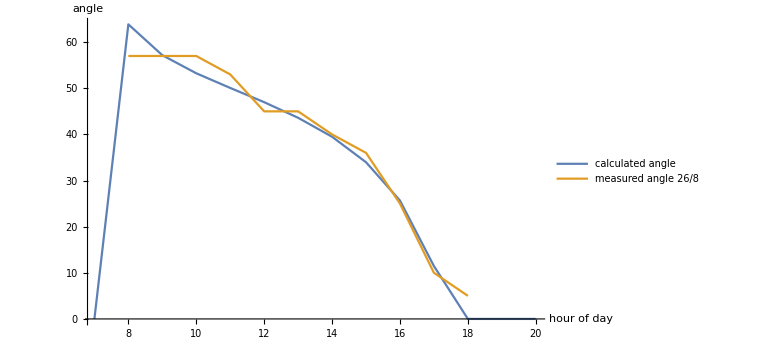

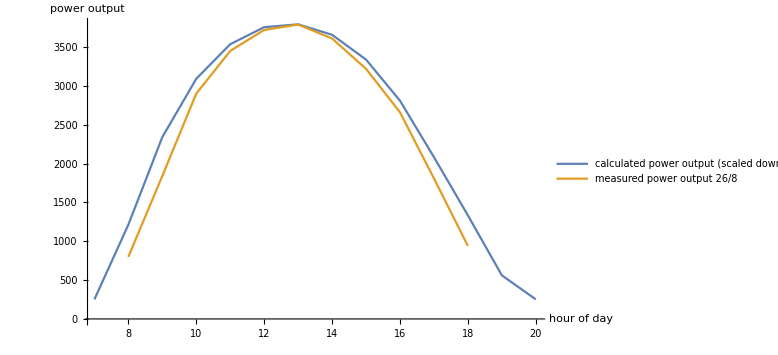

```mathematica
(* Plot measured data (angle, power output) each hour the sun is up to expected data *)
?dayAnglesHour
t = dayAnglesHour[DateObject[{2016,8,30}]]
(* 26/8 *)
measuredData2608 = {{Indeterminate,Indeterminate},{700,55},{1390,55},{2400,55},{3100,55},{3000,55},{3540,48},{Indeterminate,Indeterminate},{1900,0},{Indeterminate,0},{Indeterminate,Indeterminate},{Indeterminate,0},{Indeterminate,0},{Indeterminate,0}};
measuredData3008 = {{Indeterminate,Indeterminate},{800,57},{1840,57},{2900,57},{3450,53},{3720,45},{3790,45},{3610,40},{3220,36},{2660,25},{1810,10},{940,5},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}
hours = Table[
x,
{x,7,20}
];
ListLinePlot[{
 Transpose[{hours,t[[All,2]]}],
 Transpose[{hours,measuredData3008[[All,2]]}]
},
PlotLegends -> {"calculated angle","measured angle 26/8"},
AxesLabel -> {"hour of day","angle"}
,ImageSize -> Large]
ListLinePlot[{
Transpose[{hours,t[[All,1]]*6.6}],
Transpose[{hours,measuredData3008[[All,1]]}]
},PlotLegends -> {"calculated power output (scaled down)","measured power output 26/8"},
AxesLabel -> {"hour of day","power output"},ImageSize -> Large
]
```

csvToList[date,data] returns list of values for that date that exist in data

DateString::ambig: Warning: the interpretation of the string 09/02/2016 00:00 as a date is ambiguous.

DateObject::ambig: Warning: the interpretation of the string 09-02-2016 00:00 as a date is ambiguous.

DateString::ambig: Warning: the interpretation of the string 09/02/2016 00:15 as a date is ambiguous.

DateObject::ambig: Warning: the interpretation of the string 09-02-2016 00:15 as a date is ambiguous.

DateString::ambig: Warning: the interpretation of the string 09/02/2016 00:30 as a date is ambiguous.

General::stop: Further output of DateString::ambig will be suppressed during this calculation.

DateObject::ambig: Warning: the interpretation of the string 09-02-2016 00:30 as a date is ambiguous.

General::stop: Further output of DateObject::ambig will be suppressed during this calculation.

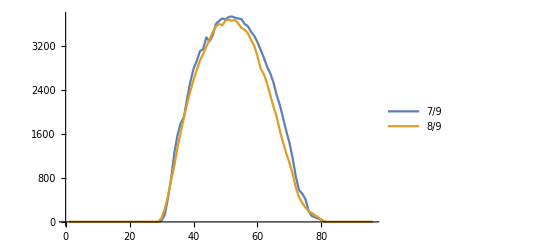

```mathematica
(************ real data ***********************)
<< SolArduino` 
(* change name of imported csv, change dates in ListLinePlot to dates exisiting in data *)

data = Import[ NotebookDirectory[]<>"data2_8.csv"];
data = Delete[data,1];
?csvToList
ListLinePlot[
{csvToList[DateObject[{2016,9,7,0,0}],data],
csvToList[DateObject[{2016,9,8,0,0}],data]},PlotLegends -> {"7/9","8/9"}
]
(*
ListLinePlot[
{
f[DateObject[{2016,8,16,0,0}]],
f[DateObject[{2016,8,17,0,0}]],
f[DateObject[{2016,8,18,0,0}]],
f[DateObject[{2016,8,19,0,0}]]
},PlotLegends -> {"24","24","40","5"}
]*)

(*ListLinePlot[
{
f[DateObject[{2016,8,17,0,0}]],
f[DateObject[{2016,8,22,0,0}]],
f[DateObject[{2016,8,23,0,0}]],
},
PlotLegends -> {"17/8","22/8","23/8"}
]*)
(*Select[data,DateDifference[DateObject[ #[[1]]],{2016,8,18,0,0} ]≤ 0 &,1 ]*)
```